```mathematica
Integrate[Cos[x w]Sin[z w]/(z w)/(8 Pi),{w,-Infinity,Infinity},GenerateConditions->False]
```

((-x+z)/(√((x-z)^2))+(x+z)/(√((x+z)^2)))/(16 z)

```mathematica
(Sign[x+z] - Sign[x-z])/(16 z)
```

(-Sign[x-z]+Sign[x+z])/(16 z)

```mathematica
a->J/(t+ t0);
```

```mathematica
Integrate[t/(a  8Pi(1+ t^2)),{t,0,a/x},GenerateConditions->False]
```

Log[1+a^2/x^2]/(16 a π)

```mathematica
1/(16 a Pi)FullSimplify[Integrate[ Log[1+a^2/x2],{x2,0,1}, GenerateConditions->Talse],{a >0}]
```

```mathematica
((1+a^2 )Log[1+a^2]-a^2Log[a^2])/(16 a π)
```

```mathematica
G[w_] =FullSimplify[ Sqrt[1/(2 Pi)]FourierCosTransform[(-a^2 Log[a^2]+(1+ a^2)Log[1+a^2])/(16 a π),a,w],{w >0}]
```

$Aborted

```mathematica
FullSimplify[ Sqrt[1/(2 Pi)]FourierCosTransform[ Log[1+a^2/x^2]/(16 a π),a,w],{x > 0}]
```

MeijerG[{{0},{1}},{{0,0,0},{1/2}},(w^2 x^2)/4]/(32 π^(3/2))

```mathematica
4/w^2Integrate[MeijerG[{{0},{1}},{{0,0,0},{1/2}},z]/(32 π^(3/2)),{z,0,w^2/4}]
```

MeijerG[{{2,2},{3}},{{2,2,2},{1,5/2}},w^2/4]/(2 π^(3/2) w^4)

```mathematica
G[w_] = MeijerG[{{2,2},{3}},{{2,2,2},{1,5/2}},w^2/4]/(2 π^(3/2) w^4);
```

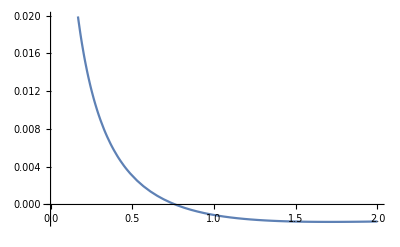

```mathematica
Plot[G[w],{w,0,2}]
```

```mathematica
wc = w/.FindRoot[G[w],{w,3/4}]
```

0.762363

```mathematica
Collect[FullSimplify[Normal[Series[MeijerG[{{2,2},{3}},{{2,2,2},{1,5/2}},w^2/4]/(2 π^(3/2) w^4),{w ,0,5}]],{w >0}],Log[w]]
```

(2+4 (-1+EulerGamma) EulerGamma)/(64 π^2)+((-4+8 EulerGamma) Log[w])/(64 π^2)+Log[w]^2/(16 π^2)

```mathematica
""
```

```mathematica
FullSimplify[Normal[Series[MeijerG[{{2,2},{3}},{{2,2,2},{1,5/2}},w^2/4]/(2 π^(3/2) w^4),{w, +Infinity, 2}]],{ w > 0}]
```

-(-1+2 EulerGamma+2 ⅈ ⅇ^-w π+2 Log[w])/(16 π^2 w^2)

```mathematica
CC[x_] = Integrate[G[w],{w,0,x}]
```

MeijerG[{{2,2},{3}},{{2,2,2},{1,3/2}},x^2/4]/(4 π^(3/2) x^3)

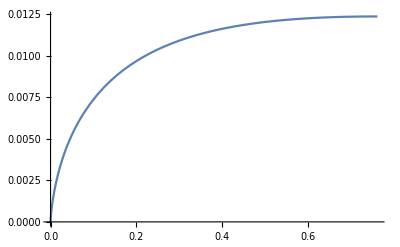

```mathematica
Plot[CC[x],{x,0,wc}]
```

```mathematica
a=.;,x=.;
```

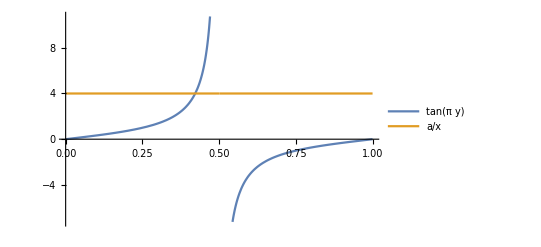

```mathematica
Plot[{Tan[Pi y],4},{y,0,1}, PlotLegends->{Tan[Pi y],a/x}]
```

```mathematica
(1 + Sign[a])/2 Log[1+a^2/x^2]/(16 a π) + (1-Sign[a])
```

```mathematica
GF =Series[((1+a^2 )Log[1+a^2]-a^2Log[a^2])/(16 a π),{a,0,11}]
```

((1-Log[a^2]) a)/(16 π)+a^3/(32 π)-a^5/(96 π)+a^7/(192 π)-a^9/(320 π)+a^11/(480 π)+O[a]^12

```mathematica
Simplify /@CoefficientList[GF,a]
```

{0,-(-1+Log[a^2])/(16 π),0,1/(32 π),0,-1/(96 π),0,1/(192 π),0,-1/(320 π),0,1/(480 π)}

```mathematica
N! Cot[Pi p/q]^(2 n)/((N-2 n)!2^(2 + 2 n))Assuming[{{q,N,n} ϵ Integers,0 < q < N, n > 0, N >2 n},Integrate[Cos[q ω]Cos[ω]^(N- 2 n) Sin[ω]^(2 n)/(2 Pi),{ω, -Pi,Pi}]]//FullSimplify
```

$Aborted

```mathematica
z = .;
```

```mathematica
Expand[(1/2( z^2 + 1))^(N- 2 n)(I/2(z^2 - 1))^(2 n),z]
```

2^-N (ⅈ (-1+z^2))^(2 n) (1+z^2)^(-2 n+N)

```mathematica
2^(-N)(-1)^n (1-z^2)^(2 n) (1+ z^2)^(N - 2 n)
```

(-1)^n 2^-N (1-z^2)^(2 n) (1+z^2)^(-2 n+N)

```mathematica
CC[N_, q_, n_] := (-1)^n 2^-N Sum[Binomial[2 n,l](-1)^l (Binomial[N-2 n,m]/.{m -> -l + (N + q)/2}), {l,0,(N+q)/2}]
```

```mathematica
FullSimplify[N(N-1) CC[N,q,1] - N CC[N,q,0]]
```

-(2^-N q^2 Gamma[1+N])/(Gamma[1/2 (2+N-q)] Gamma[1/2 (2+N+q)])

```mathematica
CC[N,q, n]
```

(-1)^n 2^-N Binomial[-2 n+N,(N+q)/2] Hypergeometric2F1[-2 n,1/2 (-N-q),1/2 (2-4 n+N-q),-1]

```mathematica
Tau[p_, q_, N_, n_] := N! Cot[Pi p/q]^(2 n)/((N-2 n)!2^(2 + 2 n))CC[N,q,n]//FullSimplify
```

```mathematica
Tau[p, q, N, n]
```

((-1)^n 2^(-1-2 n) Binomial[-2 n+N,(N+q)/2] Cot[(p π)/q]^(2 n) N! Hypergeometric2F1[1-2 n+N,1/2 (2+N-q),1/2 (2-4 n+N-q),-1])/((-2 n+N)!)

```mathematica
FullSimplify[Hypergeometric2F1[1-2 n+N,1/2 (2+N-q),1/2 (2-4 n+N-q),-1]]
```

Hypergeometric2F1[1-2 n+N,1/2 (2+N-q),1/2 (2-4 n+N-q),-1]

```mathematica
FullSimplify[(((-1)^n 2^(-1-2 n) Binomial[-2 n+N,(N+q)/2] Cot[(p π)/q]^(2 n) N!)/((-2 n+N)!))/.Binomial[X_,Y_] :> X!/(Y! (X-Y)!)]
```

((-1)^n 2^(-1-2 n) Cot[(p π)/q]^(2 n) N!)/((1/2 (-4 n+N-q))! (N+q)/2!)

```mathematica
Series[Log[Hypergeometric2F1[1-2 n+1/z,1/2 (2+(1-x )/z),1/2 (2-4 n+(1-x )/z),-1]/.{n->1}] ,{z,0,2}]
```

Log[Hypergeometric2F1[-1+1/z,1/2 (2+(1-x)/z),1/2 (-2+(1-x)/z),-1]]

```mathematica
Limit[Hypergeometric2F1[1-2 n+1/z,1-(-1+x)/(2 z),1-2 n-(-1+x)/(2 z),-1]/.{n->1},z->0,Direction->-1]
```

0

```mathematica
FullSimplify[Tau[p, q, N, 1]]
```

1/8 (-1)^n (-1+N) N Binomial[-2 n+N,(N+q)/2] Cot[(p π)/q]^2 Hypergeometric2F1[1-2 n+N,1/2 (2+N-q),1/2 (2-4 n+N-q),-1]

```mathematica
FullSimplify[Tau[p, q, N, 1]]
```

(2^(-4-N) (N-q^2) Cot[(p π)/q]^2 Gamma[1+N])/(Gamma[1/2 (2+N-q)] Gamma[1/2 (2+N+q)])

```mathematica
FullSimplify[Series[Log[Tau[N x y, N x, N, 1]],{N, Infinity,2}],{N >0, 0 < x < 1, y < 1}]
```

$Aborted

```mathematica
FullSimplify /@Collect[FunctionExpand[Normal[Series[-(N+4) Log[2] + Log[N]  + Log[1-x^2]+ LogGamma[1+N] -LogGamma[1/2 (2+N-x N)] -LogGamma[1/2 (2+N+x N)],{N, Infinity,0}]]],N]
```

1/2 (Log[N]-Log[128 π]+Log[1-x]+Log[1+x])+1/2 N ((-1+x) Log[1-x]-(1+x) Log[1+x])

```mathematica
FullSimplify[Tau[p, q, N, 3]]
```

(2^(-8-N) (15 (-4+N) (-2+N) N+(-184+15 (14-3 N) N) q^2+5 (-8+3 N) q^4-q^6) Cot[(p π)/q]^6 Gamma[1+N])/(Gamma[1/2 (2+N-q)] Gamma[1/2 (2+N+q)])

```mathematica
FullSimplify[Tau[p, q, N, 2]]
```

(2^(-6-N) (3 (-2+N) N+2 (4-3 N) q^2+q^4) Cot[(p π)/q]^4 Gamma[1+N])/(Gamma[1/2 (2+N-q)] Gamma[1/2 (2+N+q)])

```mathematica
FullSimplify[Tau[p, q, N, 4]]
```

(2^(-10-N) (105 (-6+N) (-4+N) (-2+N) N+4 (2112-7 N (424+15 (-10+N) N)) q^2+14 (176+5 N (-22+3 N)) q^4-28 (-4+N) q^6+q^8) Cot[(p π)/q]^8 Gamma[1+N])/(Gamma[1/2 (2+N-q)] Gamma[1/2 (2+N+q)])

```mathematica
FullSimplify[Tau[p, q, N,2]/Tau[p, q, N, 1]]
```

((3 (-2+N) N+2 (4-3 N) q^2+q^4) Cot[(p π)/q]^2)/(4 (N-q^2))

```mathematica
Table[Asymptotic[FullSimplify[(Tau[p, q, N,n]/Tau[p, q,  N, 1]/ Cot[(p π)/q]^(2n-2))/.q->N x, {0 < x < 1}],N->Infinity, Assumptions->0 < x < 1],{n,1,7}]/.x ->q/N
```

{1,-q^2/4,q^4/16,-q^6/64,q^8/256,-q^10/1024,q^12/4096}

```mathematica
{1,-q^2/4,q^4/16,-q^6/64,q^8/256,-q^10/1024,q^12/4096}/.q->2 z
```

{1,-z^2,z^4,-z^6,z^8,-z^10,z^12}

```mathematica
Series[1/(1 + q^2/4),{q,0,12}]
```

1-q^2/4+q^4/16-q^6/64+q^8/256-q^10/1024+q^12/4096+O[q]^13

```mathematica
Tau[p, q, N,n]/Tau[p, q,  N, 1] -> Cot[(p π)/q]^(2n-2) (-q^2/4)^(n-1)
```

```mathematica
TauS[y_, x_, N_,n_] =FullSimplify[(-q^2 /4)^(n-1) Cot[(p π)/q]^(2n) Sqrt[1-x^2]/Sqrt[128 Pi]Sqrt[N] Exp[+1/2 N ((-1+x) Log[1-x]-(1+x) Log[1+x])]/.{q -> N x, p -> N x y}]
```

(2^(-3/2-2 n) ⅇ^(1/2 N ((-1+x) Log[1-x]-(1+x) Log[1+x])) √N (-N^2 x^2)^(-1+n) √(1-x^2) Cot[π y]^(2 n))/(√π)

```mathematica
Series[(-1+x) Log[1-x]-(1+x) Log[1+x],{x,0,2}]
```

-x^2+O[x]^3

```mathematica
GG[M_, z_] =Sum[(2 M)!/(n! (2 M- 2 n)!) (I z)^n,{n,0,M}]
```

ⅈ^-M 4^M z^M HypergeometricU[-M,1/2,ⅈ/(4 z)]

```mathematica
w = .;
```

```mathematica
FullSimplify[Sum[(2 M)!/(n! ) (w^2)^( n -M)(I z)^n,{n,0,M}]]
```

(4^M ⅇ^(ⅈ w^2 z) w^(-2 M) Gamma[1/2+M] Gamma[1+M,ⅈ w^2 z])/(√π)

```mathematica
FF[M_, z_ ,w_] =(4^M ⅇ^(ⅈ w^2 z) w^(-2 M) Gamma[1/2+M] Gamma[1+M,ⅈ w^2 z])/(√π)
```

(4^M ⅇ^(ⅈ w^2 z) w^(-2 M) Gamma[1/2+M] Gamma[1+M,ⅈ w^2 z])/(√π)

```mathematica
H[u_] := u /(1 + u^2);
```

```mathematica
FullSimplify[(Integrate[H[u],{u,0,a}]/a + a Integrate[H[u]/u^2,{u,a,Infinity}, GenerateConditions->False])/(8 Pi), a >0]
```

(a^2 Log[1+1/a^2]+Log[1+a^2])/(16 a π)

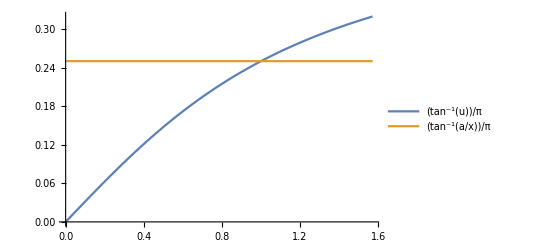

```mathematica
Plot[{ArcTan[u]/Pi,0.25},{u,0,Pi/2}, PlotLegends->{ArcTan[u]/Pi,ArcTan[a/x]/Pi}]
```

```mathematica
H0[u_] :=-8 Pi u^2 D[1/ (2 u)D[u/(1 + α^2 u^2),u],u]//FullSimplify
```

```mathematica
GGG[y_]=Integrate[4/y/(1 + α y),y]
```

4 (Log[y]-Log[1+y α])

```mathematica
NormCond =GGG[1] - GGG[1/M]//FullSimplify
```

-4 (Log[1/M]+Log[1+α]-Log[(M+α)/M])

```mathematica
α/.Solve[NormCond ==1,α ][[1]]/.M->N
```

(-ⅇ^(1/4)+N)/(-1+ⅇ^(1/4))

```mathematica
ClearAll[H1];
```

```mathematica
H1[u_, α_] = FullSimplify[u/(1+ u^2)  (4/y /(1 + α  y))/.y-> ArcTan[u]/Pi,{α >0}]
```

(4 π^2 u)/((1+u^2) ArcTan[u] (π+α ArcTan[u]))

```mathematica
AAA[u_, α_] =Normal[Series[H1[u,α],{u,0,5}]]
```

4 π-4 u α-(4 u^2 (2 π^2-3 α^2))/(3 π)+(4 u^3 (π^2 α-α^3))/π^2+(4 u^4 (26 π^4-60 π^2 α^2+45 α^4))/(45 π^3)-(4 u^5 (3 π^4 α-5 π^2 α^3+3 α^5))/(3 π^4)

```mathematica
ClearAll[BBB];
```

```mathematica
BBB[z_, α_]=Collect[FullSimplify[Normal[Series[H1[1/z,α],{z,0,5}]], { z >0}],z]
```

(64 z^2 (1+α))/(π (2+α)^2)+(16 z)/(2+α)+(16 z^4 (-16 π^3 (1+α) (2+α)^3+96 π (1+α) (2+α) (2+α (2+α))))/(3 π^4 (2+α)^5)+(16 z^3 (-3 π^4 (2+α)^4+12 π^2 (2+α)^2 (4+3 α (2+α))))/(3 π^4 (2+α)^5)+(16 z^5 (3 π^4 (2+α)^4-20 π^2 (2+α)^2 (4+3 α (2+α))+48 (16+5 α (2+α) (4+α (2+α)))))/(3 π^4 (2+α)^5)

```mathematica
QQQ[α_] := (Integrate[AAA[u,α],{u,0,a}]/a + a Integrate[BBB[z,α],{z,0,1/a}])/(8 Pi);
```

```mathematica
Collect[QQQ[α],a]
```

1/2-(a α)/(4 π)+(8 (1+α))/(3 a^2 π^2 (2+α)^2)+1/(a π (2+α))-(a^2 (2 π^2-3 α^2))/(18 π^2)+(a^3 (π^2 α-α^3))/(8 π^3)+(a^4 (26 π^4-60 π^2 α^2+45 α^4))/(450 π^4)-(a^5 (3 π^4 α-5 π^2 α^3+3 α^5))/(36 π^5)+(-(256 (1+α))/(15 π (2+α)^2)+(512 (1+α) (2+α (2+α)))/(5 π^3 (2+α)^4))/(8 a^4 π)+(-4/(2+α)+(16 (4+3 α (2+α)))/(π^2 (2+α)^3))/(8 a^3 π)+(8/(3 (2+α))-(160 (4+3 α (2+α)))/(9 π^2 (2+α)^3)+(128 (16+5 α (2+α) (4+α (2+α))))/(3 π^4 (2+α)^5))/(8 a^5 π)

```mathematica
1-0.825908
```

0.174092

```mathematica
TT[x_] =FullSimplify[1- Exp[0.0186568+0.0501143 x+0.346155 x 2+0.825908 Log[1-x]]]
```

1-1.01883 ⅇ^(0.742424 x) (1-x)^0.825908

```mathematica
PPDD[x_] = D[TT[x],x]
```

(0.841461 ⅇ^(0.742424 x))/(1-x)^0.174092-0.756406 ⅇ^(0.742424 x) (1-x)^0.825908

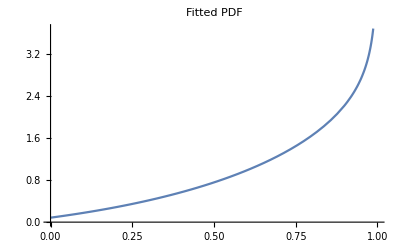

```mathematica
Plot[PPDD[x],{x,0,1},PlotLabel->"Fitted PDF"]
```

```mathematica
""
```

```mathematica
FullSimplify[-Sqrt[N]/8 Integrate[Cos[Sqrt[N]ρ z τ (b1 + b2)] Sinh[  z ρ b1]Sinh[  z ρ b2],{z,-1,1}],{τ >0, ρ >0, b1 ϵ Reals,b2 ϵ Reals}]
```

-((√N (-(b1+b2)^2 √N τ (1+N τ^2) Cosh[(b1-b2) ρ] Sin[(b1+b2) √N ρ τ]+√N τ ((b1-b2)^2+(b1+b2)^2 N τ^2) Cosh[(b1+b2) ρ] Sin[(b1+b2) √N ρ τ]+2 Cos[(b1+b2) √N ρ τ] (b2 (-b1+b2+(b1+b2) N τ^2) Cosh[b2 ρ] Sinh[b1 ρ]+b1 (b1-b2+(b1+b2) N τ^2) Cosh[b1 ρ] Sinh[b2 ρ])))/(8 (b1+b2) ρ (1+N τ^2) ((b1-b2)^2+(b1+b2)^2 N τ^2)))

```mathematica
Expand[(1/2( z^2 + 1))^(N- 2 n)(I/2(z^2 - 1))^(2 n),z]
```

```mathematica
-1/2 Cot[β/2]^2 Sin[1/4 (2 Subscript[α, m]-2 Subscript[α, n]+β (Subscript[σ, m]-Subscript[σ, n]))]^2 Subscript[σ, m] Subscript[σ, n]
```

```mathematica
X =1/4Sum[Sin[1/4 (2 β σ[m,n]+β (Subscript[σ, m]+Subscript[σ, n]))]^2 Exp[- I ω (Subscript[σ, m]+ Subscript[σ, n])] Subscript[σ, m] Subscript[σ, n],{Subscript[σ, m] ,-1,1,2},{Subscript[σ, n],-1,1,2}]//FullSimplify
```

1/4 (-1+Cos[β σ[m,n]]+ⅇ^(-2 ⅈ ω) Sin[1/2 β (1+σ[m,n])]^2+ⅇ^(2 ⅈ ω) Sin[1/2 (β-β σ[m,n])]^2)

```mathematica
Y =X/.{Sin[A_]^2 :> 1/2( 1- Cos[2 A])}//TrigToExp
```

-1/4+1/8 ⅇ^(-2 ⅈ ω)+1/8 ⅇ^(2 ⅈ ω)+1/8 ⅇ^(-ⅈ β σ[m,n])+1/8 ⅇ^(ⅈ β σ[m,n])-1/16 ⅇ^(ⅈ β+2 ⅈ ω-ⅈ β σ[m,n])-1/16 ⅇ^(-ⅈ β+2 ⅈ ω+ⅈ β σ[m,n])-1/16 ⅇ^(-2 ⅈ ω-ⅈ β (1+σ[m,n]))-1/16 ⅇ^(-2 ⅈ ω+ⅈ β (1+σ[m,n]))

```mathematica
Y[[;;3]]
```

-1/4+1/8 ⅇ^(-2 ⅈ ω)+1/8 ⅇ^(2 ⅈ ω)

```mathematica
sub={
ⅇ^(-ⅈ β σ[m,n]) ->Cos[ω]^(N-2 - m + n) Cos[ω-β]^(m-n),
ⅇ^(ⅈ β σ[m,n]) ->Cos[ω]^(N-2 - m + n) Cos[ω-β]^(m-n),
ⅇ^(ⅈ β+2 ⅈ ω-ⅈ β σ[m,n])->ⅇ^(ⅈ β+2 ⅈ ω)Cos[ω]^(N-2 - m + n) Cos[ω-β]^(m-n),
ⅇ^(-ⅈ β+2 ⅈ ω+ⅈ β σ[m,n])->ⅇ^(-ⅈ β+2 ⅈ ω)Cos[ω]^(N-2 - m + n) Cos[ω-β]^(m-n),
ⅇ^(-2 ⅈ ω-ⅈ β (1+σ[m,n]))->ⅇ^(-ⅈ β-2 ⅈ ω)Cos[ω]^(N-2 - m + n) Cos[ω-β]^(m-n),
ⅇ^(-2 ⅈ ω+ⅈ β (1+σ[m,n]))->ⅇ^(+ⅈ β-2 ⅈ ω)Cos[ω]^(N-2 - m + n) Cos[ω-β]^(m-n)
}
```

{ⅇ^(-ⅈ β σ[m,n])→Cos[β-ω]^(m-n) Cos[ω]^(-2-m+n+N),ⅇ^(ⅈ β σ[m,n])→Cos[β-ω]^(m-n) Cos[ω]^(-2-m+n+N),ⅇ^(ⅈ β+2 ⅈ ω-ⅈ β σ[m,n])→ⅇ^(ⅈ β+2 ⅈ ω) Cos[β-ω]^(m-n) Cos[ω]^(-2-m+n+N),ⅇ^(-ⅈ β+2 ⅈ ω+ⅈ β σ[m,n])→ⅇ^(-ⅈ β+2 ⅈ ω) Cos[β-ω]^(m-n) Cos[ω]^(-2-m+n+N),ⅇ^(-2 ⅈ ω-ⅈ β (1+σ[m,n]))→ⅇ^(-ⅈ β-2 ⅈ ω) Cos[β-ω]^(m-n) Cos[ω]^(-2-m+n+N),ⅇ^(-2 ⅈ ω+ⅈ β (1+σ[m,n]))→ⅇ^(ⅈ β-2 ⅈ ω) Cos[β-ω]^(m-n) Cos[ω]^(-2-m+n+N)}

```mathematica
FullSimplify[Y[[;;3]] + Y[[3;;]]/.sub]
```

1/8 (-2+3 Cos[2 ω]-2 Cos[β-ω]^(m-n) Cos[ω]^(-2-m+n+N) (-1+Cos[β] Cos[2 ω])+ⅈ Sin[2 ω])

```mathematica
FullSimplify[Y[[3;;]]/.sub]/.ⅇ^(2 ⅈ ω)->0
```

-1/4 Cos[β-ω]^(m-n) Cos[ω]^(-2-m+n+N) (-1+Cos[β] Cos[2 ω])

```mathematica
Z =TrigToExp[-1/4 Cos[β-ω]^(m-n)  (-1+Cos[β] Cos[2 ω])]/.{(ⅇ^(ⅈ β-ⅈ ω)+ⅇ^(-ⅈ β+ⅈ ω))^(m-n)-> Binomial[m-n,l] ⅇ^((ⅈ β-ⅈ ω)(m-n-l)+ I(ω-β)l)}
```

-2^(-2-m+n) ⅇ^((-l+m-n) (ⅈ β-ⅈ ω)+ⅈ l (-β+ω)) (-1+1/4 (ⅇ^(-ⅈ β)+ⅇ^(ⅈ β)) (ⅇ^(-2 ⅈ ω)+ⅇ^(2 ⅈ ω))) Binomial[m-n,l]

```mathematica
Z=FullSimplify[Z]/.Cos[2 ω] -> 1/2( E^(2I ω) + E^(-2I ω))//Expand
```

2^(-2-m+n) ⅇ^(-ⅈ (2 l-m+n) (β-ω)) Binomial[m-n,l]-2^(-3-m+n) ⅇ^(-ⅈ (2 l-m+n) (β-ω)-2 ⅈ ω) Binomial[m-n,l] Cos[β]-2^(-3-m+n) ⅇ^(-ⅈ (2 l-m+n) (β-ω)+2 ⅈ ω) Binomial[m-n,l] Cos[β]

```mathematica
ClearAll[subInt];
```

```mathematica
subInt[r_, l_] = {E^(X_) F_:> (F/.Solve[D[X,ω]==I r,l][[1]])}
```

{ⅇ^X_ F_:>(F/.Solve[∂_ω X==ⅈ r,l]⟦1⟧)}

```mathematica
JJ[r_] =FullSimplify[Z/.subInt[r,l]]
```

2^(-3-m+n) (2 Binomial[m-n,1/2 (m-n+r)]-(Binomial[m-n,1/2 (-2+m-n+r)]+Binomial[m-n,1/2 (2+m-n+r)]) Cos[β])

```mathematica
HH =FullSimplify[E^(I ω q)TrigToExp[Cos[ω]^(-2-m+n+N)]/.(ⅇ^(-ⅈ ω)+ⅇ^(ⅈ ω))^L_ :> Binomial[L,s]E^( I ω s - I ω(L-s))]
```

2^(2+m-n-N) ⅇ^(ⅈ (2+m-n-N+q+2 s) ω) Binomial[-2-m+n+N,s]

```mathematica
HH0=HH/.subInt[-r,s]
```

2^(2+m-n-N) Binomial[-2-m+n+N,1/2 (-2-m+n+N-q-r)]

```mathematica
AAA =FullSimplify[(HH0 JJ[r])/.r-> n-m+ 2l]
```

2^(-1-N) Binomial[-2-m+n+N,1/2 (-2-2 l+N-q)] (2 Binomial[m-n,l]-(Binomial[m-n,-1+l]+Binomial[m-n,1+l]) Cos[β])

```mathematica
Binomial[m-n,l]FullSimplify[Binomial[m-n,-1+l]/Binomial[m-n,l]]
```

-(l Binomial[m-n,l])/(-1+l-m+n)

```mathematica
Binomial[m-n,l]FullSimplify[(2 -(Binomial[m-n,-1+l]+Binomial[m-n,1+l])/Binomial[m-n,l] Cos[β])]
```

Binomial[m-n,l] (2+(l Cos[β])/(-1+l-m+n)+((l-m+n) Cos[β])/(1+l))

```mathematica
BBB = 2^(-1-N) Sum[Binomial[-2-m+n+N,1/2 (-2-2 l+N-q)] Binomial[m-n,l] (2+(l Cos[β])/(-1+l-m+n)+((l-m+n) Cos[β])/(1+l)),{l , 0,m-n}];
```

```mathematica
BBB =FullSimplify[BBB]
```

2^(-2-N) Gamma[-1-m+n+N] ((2 Cos[β])/(Gamma[-1-m+n+N/2-q/2] Gamma[1/2 (2+N+q)])+((2-N+q) Cos[β] Hypergeometric2F1Regularized[-m+n,1-N/2-q/2,-m+n+N/2-q/2,1])/Gamma[1/2 (2+N+q)]+((2 Cos[β])/Gamma[1/2 (-2-2 m+2 n+N+q)]-(-2 N+2 q+(-2+N+q) Cos[β]) Hypergeometric2F1Regularized[-m+n,1/2 (2-N+q),1/2 (-2 m+2 n+N+q),1])/Gamma[1/2 (2+N-q)])

```mathematica
Ans =FullSimplify[ -1/2 Cot[β/2]^2 BBB]
```

-2^(-3-N) Cot[β/2]^2 Gamma[-1-m+n+N] ((2 Cos[β])/(Gamma[-1-m+n+N/2-q/2] Gamma[1/2 (2+N+q)])+((2-N+q) Cos[β] Hypergeometric2F1Regularized[-m+n,1-N/2-q/2,-m+n+N/2-q/2,1])/Gamma[1/2 (2+N+q)]+((2 Cos[β])/Gamma[1/2 (-2-2 m+2 n+N+q)]-(-2 N+2 q+(-2+N+q) Cos[β]) Hypergeometric2F1Regularized[-m+n,1/2 (2-N+q),1/2 (-2 m+2 n+N+q),1])/Gamma[1/2 (2+N-q)])

```mathematica
A = (2 Cos[β])/(Gamma[-1-m+n+N/2-q/2] Gamma[1/2 (2+N+q)])+((2-N+q) Cos[β] Hypergeometric2F1Regularized[-m+n,1-N/2-q/2,-m+n+N/2-q/2,1])/Gamma[1/2 (2+N+q)]
```

```mathematica
B = ((2 Cos[β])/Gamma[1/2 (-2-2 m+2 n+N+q)]-(-2 N+2 q+(-2+N+q) Cos[β]) Hypergeometric2F1Regularized[-m+n,1/2 (2-N+q),1/2 (-2 m+2 n+N+q),1])/Gamma[1/2 (2+N-q)]
```

```mathematica
-2^(-3-N) Cot[β/2]^2 Gamma[-1-m+n+N] (a + b + c + d)
```

```mathematica
a = (2 Cos[β])/(Gamma[-1-m+n+N/2-q/2] Gamma[1/2 (2+N+q)])
```

```mathematica
b = ((2-N+q) Cos[β] Hypergeometric2F1Regularized[-m+n,1-N/2-q/2,-m+n+N/2-q/2,1])/Gamma[1/2 (2+N+q)]
```

```mathematica
c = (2 Cos[β])/Gamma[1/2 (-2-2 m+2 n+N+q)]/Gamma[1/2 (2+N-q)]
```

(2 Cos[β])/(Gamma[1/2 (2+N-q)] Gamma[1/2 (-2-2 m+2 n+N+q)])

```mathematica
d = (-(-2 N+2 q+(-2+N+q) Cos[β]) Hypergeometric2F1Regularized[-m+n,1/2 (2-N+q),1/2 (-2 m+2 n+N+q),1])/Gamma[1/2 (2+N-q)]
```